```mathematica
Clear[y,sols,sols1,sols2,y];
```

```mathematica
DSolveValue[{y''[x]==-1/(1+ϵ *y[x])^2,y[0]==0,y'[0]==7},y[x],x]
```

DSolveValue::bvimp: General solution contains implicit solutions. In the boundary value problem, these solutions will be ignored, so some of the solutions will be lost.

DSolveValue[{y''[x]==-1/(1+ϵ y[x])^2,y[0]==0,y'[0]==7},y[x],x]

We apply the shooting method so we can plot the exact solution for the ODEs for different values of ϵ

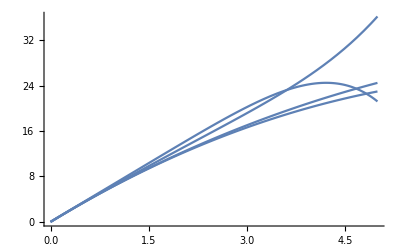

```mathematica
sols = NDSolve[{y''[x]==-1/(1+0.002 *y[x])^2,y[0]==0,y'[0]==7},y,{x,0,1}, Method->{"Shooting"}];
sols1= NDSolve[{y''[x]==-1/(1+0.01*y[x])^2,y[0]==0,y'[0]==7},y,{x,0,1}, Method->{"Shooting"}];
sols2= NDSolve[{y''[x]==-1/(1+y[x])^2,y[0]==0,y'[0]==7},y,{x,0,1}, Method->{"Shooting"}];
sols3= NDSolve[{y''[x]==-1/(1+0.1*y[x])^2,y[0]==0,y'[0]==7},y,{x,0,1}, Method->{"Shooting"}];
Show[Plot[Evaluate[y[x] /. sols], {x,0,5},PlotRange->All],Plot[Evaluate[y[x]/.sols1],{x,0,5},PlotRange->All],Plot[Evaluate[y[x]/.sols2],{x,0,5},PlotRange->All],Plot[Evaluate[y[x]/.sols3],{x,0,5},PlotRange->All]]
```

we expand the left hand side of the equation

```mathematica
Series[-1/((1+y)^2),{y,0,5}]
```

-1+2 y-3 y^2+4 y^3-5 y^4+6 y^5+O[y]^6

```mathematica
Normal[-1+2 y-3 y^2+4 y^3-5 y^4+6 y^5+O[y]^6]
```

-1+2 y-3 y^2+4 y^3-5 y^4+6 y^5

```mathematica
(*y0''[x]+ϵy1''[x]+ϵ^2  y2''[x]+y3''[x]=-1+2ϵ (y0[x]+ϵy1[x]+ϵ^2y2[x])-3ϵ^2(y0[x]+ϵy1[x]+ϵ^2y2[x])*)
```

```mathematica
DSolve [{y''[x]==-1,y[0]==0,y'[0]==7},y[x],x]
```

{{y[x]→1/2 (14 x-x^2)}}

```mathematica
DSolve[{y''[x]== (14 x-x^2),y[0]==0,y'[0]==0},y[x],x]
```

{{y[x]→1/12 (28 x^3-x^4)}}

```mathematica
Clear[y]
```

```mathematica
DSolve[{y''[x]== 3/2(14 x-x^2)-1/6(28 x^3-x^4),y[0]==0,y'[0]==0},y[x],x]
```

{{y[x]→1/360 (1260 x^3-45 x^4-84 x^5+2 x^6)}}

We join the three terms asymptotic expansion, and plot it for different values of epsillon

```mathematica
y[x_]:=7x-(x^2)/2+ϵ(7/3 x^3-1/12 x^4)+ϵ^2 (x^4/8 - 21x^3/3 + 14x^5/30  - x^6/180)
```

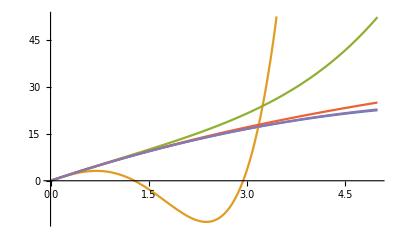

```mathematica
Plot[Evaluate[Table[y[x],{ϵ,{0,1,1/10,1/100,1/1000}}]],{x,0,5}]
```